# Simple Quantum Tunneling Effect ( WKB )

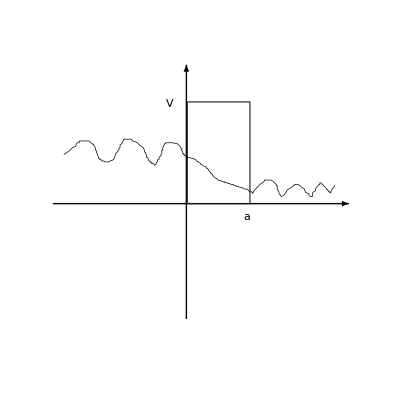

```mathematica
(* assume the V[x] varies slowly in a wavelentgh *)
```

```mathematica
(* the Schrodinger equation *)
D[ψ[x],x]==-p^2/ℏ^2 ψ[x]
p^2= 2m (Ee-V[x])
```

```mathematica
(* The general solution of wavefunction take the form *)
ψ[x_] :=A[x]Exp[ⅈ ϕ[x]]
```

```mathematica
Collect[D[ψ[x],{x,2}],Exp[ⅈ ϕ[x]]]
```

ⅇ^(ⅈ ϕ[x]) (2 ⅈ A'[x] ϕ'[x]-A[x] ϕ'[x]^2+A''[x]+ⅈ A[x] ϕ''[x])

```mathematica
2 ⅈ A'[x] ϕ'[x]-A[x] ϕ'[x]^2+A''[x]+ⅈ A[x] ϕ''[x]==-p^2/ℏ^2 A[x]
```

```mathematica
A''[x]==(ϕ'[x]^2-p^2/ℏ^2)A[x]
2  A'[x] ϕ'[x]+ A[x] ϕ''[x]==0  ⇒  D[A[x]^2 ϕ'[x],x]==0
```

```mathematica
D[A[x]^2 ϕ'[x],x]==0
⇒ A[x]=C/(√ϕ'[x])
```

```mathematica
(* using the Approx *)
(* A''[x] == 0 *)
ϕ'[x]==±p/ℏ
⇒ ϕ[x_]:= ±1/ℏ∫p[x]dx=±∫√((2m)/ℏ(Ee-V[x]))ⅆx
```

```mathematica
ψ[x_]:=C/(√(√(2m (Ee-V[x]))))Exp[ⅈ∫√((2m)/ℏ(Ee-V[x]))ⅆx]
```

```mathematica
(* out side the Barrier *)
ψA[x_]:=Exp[ⅈ k x]+BA Exp[-ⅈ k x ]
ψC[x_]:=FC Exp[ⅈ k x]
```

```mathematica
(* inside the barrier *)
ψB[x_]:=C2/(√(√(2m (V[x]-Ee))))Exp[-∫√((2m)/ℏ(V[x]-Ee))ⅆx]
```

```mathematica
(* for the potential is high or long *)
(* the decay is mainly govn by the decay *)
(* the trasmission is *)
T = Exp[-2∫_0^a √((2m)/ℏ(V[x]-Ee))dx]
```

```mathematica
(* for constant V[x] = Vo
```

```mathematica
∫_0^a √(Vo-Ee)ⅆx
```

a √(-Ee+Vo)